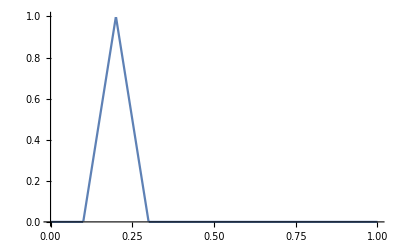

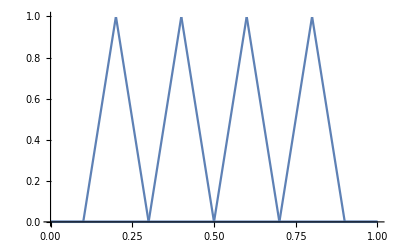

0

361/15000

{41/15000,161/15000,361/15000,641/15000}

```mathematica
Block[
{n=5,k,Ω,ξ},
Ω=Table[Piecewise[{{2n ξ-2k+1,(2k-1)/2/n<ξ≤k/n},{2k+1-2n ξ,k/n<ξ≤(2k+1)/2/n},{0,True}}],{k,1,n-1}];
Print[Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]];
Show[
Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[2]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[3]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[4]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]
]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[2]],{ξ,0,1}]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[3]],{ξ,0,1}]//Print;
Table[Integrate[ξ^2 Ω[[k]]Ω[[k]],{ξ,0,1}],{k,1,n-1}]//Print;
]
```

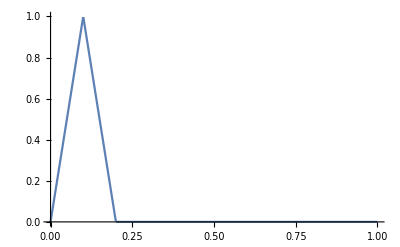

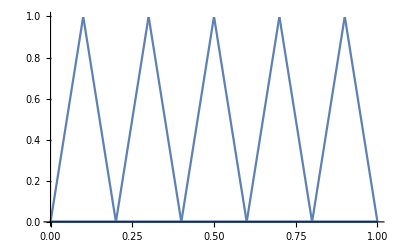

0

251/15000

{11/15000,91/15000,251/15000,491/15000,811/15000}

```mathematica
Block[
{n=5,k,Ω,ξ},
Ω=Table[Piecewise[{{2n ξ-2k+2,(k-1)/n<ξ≤(2k-1)/2/n},{2k-2n ξ,(2k-1)/2/n<ξ≤k/n},{0,True}}],{k,1,n}];
Print[Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]];
Show[
Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[2]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[3]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[4]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[5]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]
]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[2]],{ξ,0,1}]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[3]],{ξ,0,1}]//Print;
Table[Integrate[ξ^2 Ω[[k]]Ω[[k]],{ξ,0,1}],{k,1,n}]//Print;
]
```

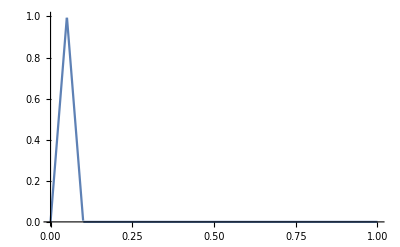

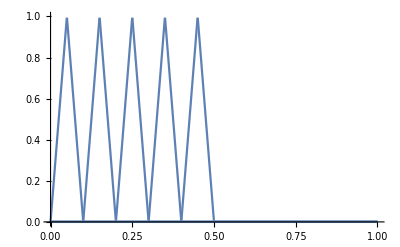

0

251/120000

{0.0000916667,0.000758333,0.00209167,0.00409167,0.00675833,0.0100917,0.0140917,0.0187583,0.0240917,0.0300917}

```mathematica
Block[
{n=10,k,Ω,ξ},
Ω=Table[Piecewise[{{2n ξ-2k+2,(k-1)/n<ξ≤(2k-1)/2/n},{2k-2n ξ,(2k-1)/2/n<ξ≤k/n},{0,True}}],{k,1,n}];
Print[Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]];
Show[
Plot[Ω[[1]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[2]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[3]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[4]],{ξ,0,1},PlotRange->{{0,1},{0,1}}],
Plot[Ω[[5]],{ξ,0,1},PlotRange->{{0,1},{0,1}}]
]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[2]],{ξ,0,1}]//Print;
Integrate[ξ^2 Ω[[3]]Ω[[3]],{ξ,0,1}]//Print;
Table[Integrate[ξ^2 Ω[[k]]Ω[[k]],{ξ,0,1}]//N,{k,1,n}]//Print;
]
```

```mathematica
Integrate[2n ξ^3-(2m-2)ξ^2,{ξ,(m-1)/n,(2m-1)/(2n)}]//FullSimplify
```

(11+8 m (-4+3 m))/(96 n^3)

```mathematica
Integrate[2m ξ^2-2 n ξ^3,{ξ,(2m-1)/(2n),m/n}]//FullSimplify
```

(3+8 m (-2+3 m))/(96 n^3)

```mathematica
((11+8 m (-4+3 m))/(96 n^3)+(3+8 m (-2+3 m))/(96 n^3))//Together
```

(7-24 m+24 m^2)/(48 n^3)

```mathematica
Integrate[4n^2 ξ^2,{ξ,(m-1)/n,m/n}]//Together
```

(4 (1-3 m+3 m^2))/(3 n)

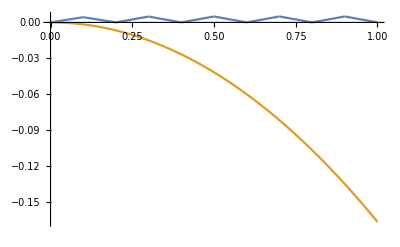

```mathematica
Block[
{m,n=5,ξ,θ,θact},
θ[ξ_]:=Sum[(24m^2-24m+7)/(64 n^2)/(3m^2-3m+1)Piecewise[{{2n ξ-2m+2,(m-1)/n<ξ≤(2m-1)/2/n},{2m-2n ξ,(2m-1)/2/n<ξ≤m/n},{0,True}}],{m,1,n}];
θact[ξ_]:=-ξ^2/6;
Plot[{θ[ξ],θact[ξ]},{ξ,0,1}]
]
```

```mathematica
Block[
{k,n=10,ξ,ω,A=2},
ω=Table[Piecewise[{{A(1-ξ),(k-1)/n≤ξ<k/n},{0,True}}],{k,1,n}];
Integrate[ω[[1]]ω[[2]],{ξ,0,1}]//Print;
Integrate[ω[[4]]ω[[5]],{ξ,0,1}]//Print;
Integrate[ω[[4]]ω[[4]],{ξ,0,1}]//Print;
D[ω,ξ]//Print;
]
```

0

0

127/750

{Piecewise[{{0, ξ<0}, {-2, 0<ξ<1/10}, {0, ξ>1/10}, {Indeterminate, True}}],Piecewise[{{0, ξ<1/10}, {-2, 1/10<ξ<1/5}, {0, ξ>1/5}, {Indeterminate, True}}],Piecewise[{{0, ξ<1/5}, {-2, 1/5<ξ<3/10}, {0, ξ>3/10}, {Indeterminate, True}}],Piecewise[{{0, ξ<3/10}, {-2, 3/10<ξ<2/5}, {0, ξ>2/5}, {Indeterminate, True}}],Piecewise[{{0, ξ<2/5}, {-2, 2/5<ξ<1/2}, {0, ξ>1/2}, {Indeterminate, True}}],Piecewise[{{0, ξ<1/2}, {-2, 1/2<ξ<3/5}, {0, ξ>3/5}, {Indeterminate, True}}],Piecewise[{{0, ξ<3/5}, {-2, 3/5<ξ<7/10}, {0, ξ>7/10}, {Indeterminate, True}}],Piecewise[{{0, ξ<7/10}, {-2, 7/10<ξ<4/5}, {0, ξ>4/5}, {Indeterminate, True}}],Piecewise[{{0, ξ<4/5}, {-2, 4/5<ξ<9/10}, {0, ξ>9/10}, {Indeterminate, True}}],Piecewise[{{0, ξ<9/10}, {-2, 9/10<ξ<1}, {0, ξ>1}, {Indeterminate, True}}]}

```mathematica
Coefficient[D[(ξ-1)((2A-4B)ξ-A),ξ],ξ]
```

4 A-8 B

```mathematica
(D[(ξ-1)((2A-4B)ξ-A),ξ]-Coefficient[D[(ξ-1)((2A-4B)ξ-A),ξ],ξ]ξ)//FullSimplify
```

-3 A+4 B

0

0

45436/46875

1256891/6562500

{Piecewise[{{6-16 ξ, 0<ξ<1/10}, {0, 10 ξ>1||ξ<0}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 1/10<ξ<1/5}, {0, 5 ξ>1||10 ξ<1}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 1/5<ξ<3/10}, {0, 10 ξ>3||5 ξ<1}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 3/10<ξ<2/5}, {0, 5 ξ>2||10 ξ<3}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 2/5<ξ<1/2}, {0, 2 ξ>1||5 ξ<2}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 1/2<ξ<3/5}, {0, 5 ξ>3||2 ξ<1}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 3/5<ξ<7/10}, {0, 10 ξ>7||5 ξ<3}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 7/10<ξ<4/5}, {0, 5 ξ>4||10 ξ<7}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 4/5<ξ<9/10}, {0, 10 ξ>9||5 ξ<4}, {Indeterminate, True}}],Piecewise[{{6-16 ξ, 9/10<ξ<1}, {0, ξ>1||10 ξ<9}, {Indeterminate, True}}]}

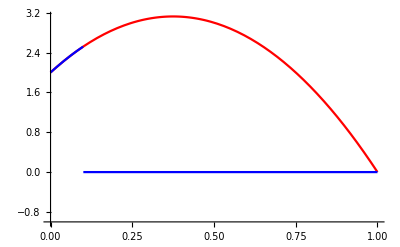

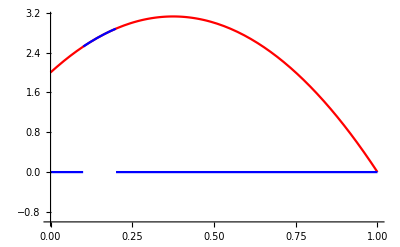

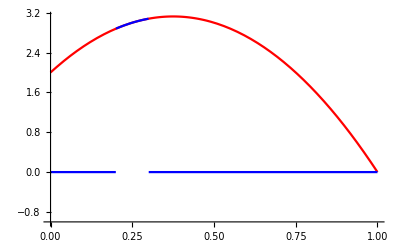

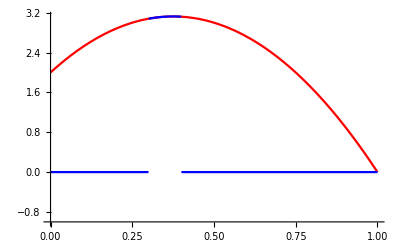

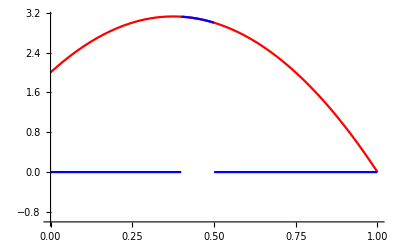

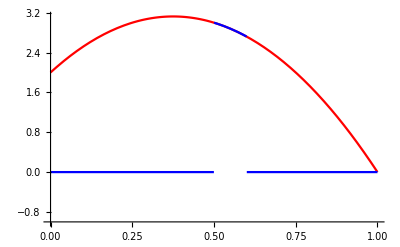

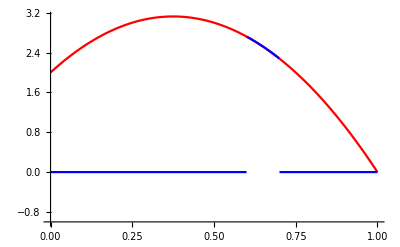

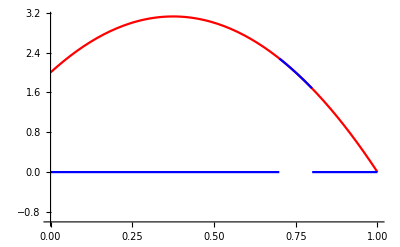

```mathematica
Block[
{k,n=10,ξ,ω,A=2,B=3},
ω=Table[Piecewise[{{(ξ-1)((2A-4B)ξ-A),(k-1)/n≤ξ≤k/n},{0,True}}],{k,1,n}];
Integrate[ω[[1]]ω[[2]],{ξ,0,1}]//Print;
Integrate[ξ^2 ω[[4]]ω[[5]],{ξ,0,1}]//Print;
Integrate[ω[[4]]ω[[4]],{ξ,0,1}]//Print;
Integrate[ξ^2ω[[5]]ω[[5]],{ξ,0,1}]//Print;
D[ω,ξ]//FullSimplify//Print;
For[
k=1,k≤n,k++,
Plot[{(ξ-1)((2A-4B)ξ-A),ω[[k]]},{ξ,0,1},PlotStyle->{Red,Blue},AxesOrigin->{0,-1}]//Print;
]
]
```

```mathematica
Block[
{n=3,k,m,Ω,ξ,A,X,x,y,z},
Ω=Table[Piecewise[{{2n ξ-2k+2,(k-1)/n<ξ≤(2k-1)/2/n},{2k-2n ξ,(2k-1)/2/n<ξ≤k/n},{0,True}}],{k,1,n}];
A=Table[Table[Integrate[2/ξ D[Ω[[k]],ξ]Ω[[m]],{ξ,0,1}]-If[k==m,Integrate[Ω[[k]]^2+D[Ω[[k]],ξ]^2,{ξ,0,1}],0],{m,1,n}],{k,1,n}];
X={x,y,z};
Print[N[A]//MatrixForm];
Print[N[A].X];
(*ContourPlot3D[A.X==0,{x,-1,1},{y,-1,1},{z,-1,1}]*)
ContourPlot3D[3x+2y+z==8,{x,-10,10},{y,-10,10},{z,-10,10}]
]
```

(-4.74664 | 0. | 0.
0. | -11.651 | 0.
0. | 0. | -11.9492)

{0.-4.74664 x,0.-11.651 y,0.-11.9492 z}

-Graphics3D-

```mathematica
Block[
{n=3,k,m,Ω,ξ,A=2,B=3,X,x,y,z},
Ω=Table[Piecewise[{{(ξ-1)((2A-4B)ξ-A),(k-1)/n≤ξ≤k/n},{0,True}}],{k,1,n}];
A=Table[Table[Integrate[2/ξ D[Ω[[k]],ξ]Ω[[m]],{ξ,0,1}]-If[k==m,Integrate[Ω[[k]]^2+D[Ω[[k]],ξ]^2,{ξ,0,1}],0],{m,1,n}],{k,1,n}];
X={x,y,z};
Print[N[A]//MatrixForm];
Print[N[A].X];
ContourPlot3D[3x+2y+z==8,{x,-10,10},{y,-10,10},{z,-10,10}]//Print;
(*ContourPlot3D[A.X==0,{x,-1,1},{y,-1,1},{z,-1,1}]*)
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {4.08043×10^-226}. NIntegrate obtained 4.59868×10^6 and 3.84908×10^6 for the integral and error estimates.

(4.59868×10^6 | 0. | 0.
0. | -11.5653 | 0.
0. | 0. | -27.0623)

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {4.08043×10^-226}. NIntegrate obtained 4.59868×10^6 and 3.84908×10^6 for the integral and error estimates.

{0.+4.59868×10^6 x,0.-11.5653 y,0.-27.0623 z}

-Graphics3D-

```mathematica
Block[
{n=10,k,m,Ω,ξ,A,X,x,y,z},
Ω=Table[Piecewise[{{n ξ-k+1,(k-1)/n<ξ≤k/n},{k+1-n ξ,k/n<ξ≤(k+1)/n},{0,True}}],{k,1,n}];
A=Table[Table[-Integrate[2/ξ D[Ω[[k]],ξ]Ω[[m]],{ξ,0,1}]+Integrate[Ω[[k]]Ω[[m]]+D[Ω[[k]],ξ]D[Ω[[m]],ξ],{ξ,0,1}],{m,1,n}],{k,1,n}];
X={x,y,z};
Print[N[A]//MatrixForm];
Print[Det[A]//N];
]
```

(7.79255 | -3.84628 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-17.7092 | 18.2575 | -6.20194 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -14.3112 | 19.2998 | -7.24426 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -12.9979 | 19.6419 | -7.83482 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -12.2977 | 19.7967 | -8.21549 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -11.8619 | 19.8799 | -8.48141 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -11.5644 | 19.9298 | -8.67773 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -11.3484 | 19.962 | -8.82862 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -11.1843 | 19.9841 | -8.94823
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -11.0554 | 8.99823)

-2.43629×10^8